| {"Frank",α} | log_α((∏_i^n (α^u_i-1))/(α-1)^(n-1)+1) | Frank copula
For "Frank", α can be any positive number in two dimensions and any positive number less than or equal to a certain constant α_max(d)>1 for dimensions higher than two. 

From Nelsen:


From SRM paper:

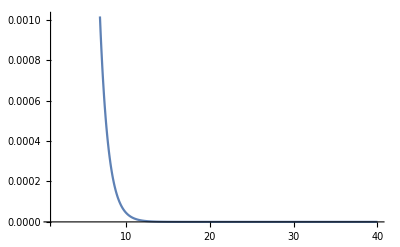

```mathematica
Plot[Exp[-θ], {θ,1,40}]
```

```mathematica
data=Import[NotebookDirectory[] <> "../processed_data/coingecko_future_v3/train/0.csv"];
```

```mathematica
data⟦1;;10⟧
```

( | Date | bitcoin price | Close | log return bitcoin | log return future
5 | 2021-01-27 | 31038.2 | 31905. | -0.0310281 | -0.0204754
6 | 2021-01-26 | 32016.3 | 32565. | -0.0128355 | -0.0492799
7 | 2021-01-25 | 32429.9 | 34210. | -0.0323413 | -0.00160643
8 | 2021-01-22 | 33495.9 | 34265. | 0.0683149 | 0.0507328
9 | 2021-01-21 | 31284. | 32570. | -0.110154 | -0.0966491
10 | 2021-01-20 | 34927.1 | 35875. | -0.041842 | -0.0462983
11 | 2021-01-19 | 36419.5 | 37575. | 0.0068495 | 0.0280682
12 | 2021-01-15 | 36170.9 | 36535. | -0.0686241 | -0.103525
13 | 2021-01-14 | 38740.2 | 40520. | 0.0316585 | 0.0819984)

```mathematica
r=data⟦2;;All,5;;6⟧;
u=hatF[r⟦1;;All,1⟧];
v=hatF[r⟦1;;All,2⟧];
```

```mathematica
Clear[α]
```

```mathematica
dist = CopulaDistribution[{"Frank", α}, {UniformDistribution[], UniformDistribution[]}];
```

```mathematica
Total[Table[Log[PDF[dist/.{α->0.5},{u⟦k⟧,v⟦k⟧}]],{k,1,Length[u]}]]
```

30.7855

```mathematica
NMaximize[{Total[Table[Log[PDF[dist,{u⟦k⟧,v⟦k⟧}]],{k,1,Length[u]}]],0<α},α]
```

{300.029,{α→4.80243×10^-8}}

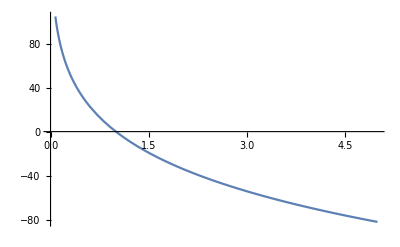

```mathematica
Plot[Total[Table[Log[PDF[dist,{u⟦k⟧,v⟦k⟧}]],{k,1,Length[u]}]], {α,0,5}]
```

Frank

```mathematica
Correlation[u,v]
```

0.929674

16.8516

0.942547

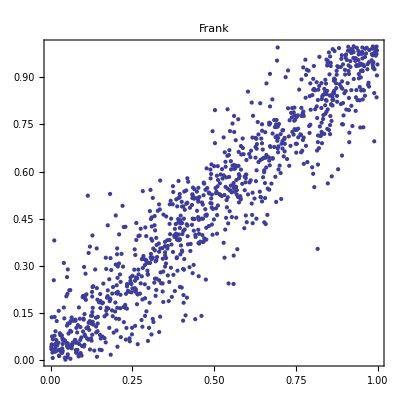

```mathematica
α=0.001199;
α=10^(-1);
α=4.802428708113742*^-8;
-Log[α]
frank = CopulaDistribution[{"Frank", α}, {UniformDistribution[], UniformDistribution[]}];
sp[frank]
r4=RandomVariate[frank, 1000];
p4=ListPlot[r4,PlotTheme->"Classic", PlotStyle->Thick,Frame->True, PlotLabel->"Frank", AspectRatio->1]
```